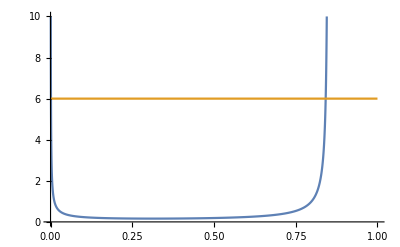

```mathematica
U=50;ra=85/100;E1[rb_]:=U/(rb Log[ra/rb]);
Plot[{E1[rb]/1000,6},{rb,0,1},PlotRange->{Full,{0,10}}]
```

```mathematica
{(U/(rb Log[ra/rb]))/1000==6}~Reduce~rb
%//N
```

rb==17/20 ⅇ^ProductLog[-1/102]||rb==17/20 ⅇ^ProductLog[-1,-1/102]

rb==0.841625||rb==0.0012828